```mathematica
SetAttributes[tex,HoldFirst]
tex[exp_]:=TeXForm[HoldForm[exp]]
tf:=TableForm
mf:=MatrixForm
df:=Defer
```

```mathematica
Product[Sin[(π k/n)],{k,1,n-1}]
```

2^(1-n) n

```mathematica
Product[Gamma[k/n+1]/(k/n),{k,1,n-1}]//(TraditionalForm[Sqrt[#^2]]&)
```

√((2 π)^(n-1)/n)

```mathematica
ClearAll[Li];
Li[x_]:=Integrate[1/Log[y],{y,2,x}]
Li[20.]//N
```

8.86014

```mathematica
LogIntegral[20.]-LogIntegral[2.]
```

8.86014

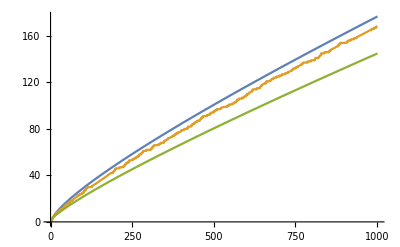

```mathematica
Plot[{LogIntegral[y]-LogIntegral[2],PrimePi[y],y/Log[y]},{y,2,1001},AxesOrigin->{0,0}]
```

```mathematica
D[Log[Log[y]],y]
```

1/(y Log[y])

```mathematica
ClearAll[f];
D[Log[f[x]],x]
```

f'[x]/f[x]

# Analytic Number Theory

Foundations

## Arithmetic [ToDo]: Indeling

## Tools [ToDo]: Indeling

Arithmetic Functions and Dirichlet Series

The Prime Number Theorem

Dirichlet’s Theorem

Error Estimates and the Riemann Hypothesis

Temp

## Tmp-1